NB: Sending χ→-χ to flip plot the right way round

ω_s<<ω_FSR?: ω_s=37500., ω_FSR=7500

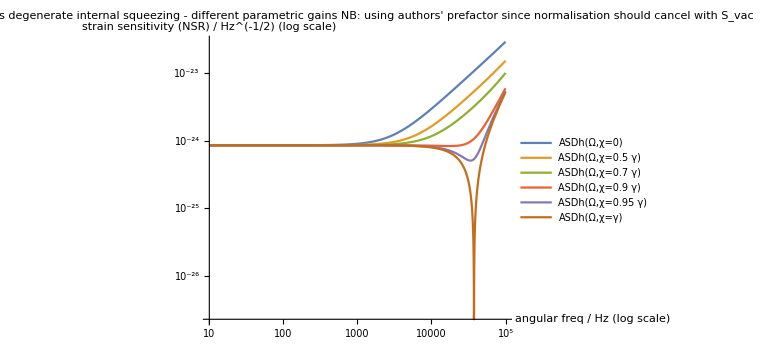

```mathematica
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
(*Using the same values as Fig.3 in Korobko et al, 2019: benchmark 3rd generation detector*)
λ=1550 10^-9(*m*);
w0=c/λ;
P = 4 10^6(*W*);
Larm=20 10^3(*m*);
Lse=56(*m*);
Titm=0.07;
Tse=0.35;
ws=c(Titm/(4 Lse Larm))^(1/2);
Print[StringForm["ω_s<<ω_FSR?: ω_s=``, ω_FSR=``",ws,c/(2 Larm)]]
γ=(c Tse)/(4 Lse);
(*the authors don't say what value they use for χ, threshold?*)
Sh[Ω_,χ_]:=(ℏ c)/(8 P Larm w0)(Ω^2(γ-χ)^2+(ws^2-Ω^2)^2)/(ws^2 γ)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
LogLogPlot[{ASDh[Ω,χ=0],ASDh[Ω,χ=0.5γ],ASDh[Ω,χ=0.7γ],ASDh[Ω,χ=0.9γ],ASDh[Ω,χ=0.95γ],ASDh[Ω,χ=γ]},{Ω,10,10^5},AxesLabel->{"angular freq / Hz (log scale)", "strain sensitivity (NSR) / Hz^(-1/2) (log scale)"},ImageSize->Large,PlotRange->All,PlotLegends->"Expressions",PlotLabel->"lossless degenerate internal squeezing - different parametric gains\nNB: using authors' prefactor since normalisation should cancel with S_vac"]
```

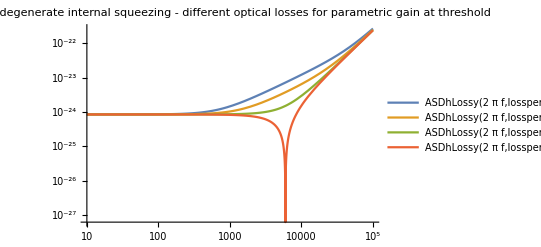
-Graphics-non-angular freq, f / Hz (log scale)strain sensitivity (NSR) / Hz^(-1/2) (log scale)

```mathematica
(*Lossy result*)
χ=γ;(*at threshold*)
kout=γ;
(*loss=kloss/(kloss+kout),(kout*loss)/(1-loss)=kloss*)
(*have omitted factor 1/2 since it should have cancelled with quadrature normalisation in Subscript[S, vac]*)
ShLossy[Ω_,losspercen_]:=(ℏ c)/(8 P Larm w0)(Ω^2((kout+(kout*losspercen/100)/(1-losspercen/100)+χ)^2-4kout χ)+(ws^2-Ω^2)^2)/(ws^2 kout)
ASDhLossy[Ω_,losspercen_]:=Abs[ShLossy[Ω,losspercen]]^(1/2)
Labeled[LogLogPlot[{
ASDhLossy[2π f,losspercen=10],
ASDhLossy[2π f,losspercen=3],
ASDhLossy[2π f,losspercen=0.5],
ASDhLossy[2π f,losspercen=0]},{f,10,10^5},ImageSize->400,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing - different optical losses\nfor parametric gain at threshold"],{"non-angular freq, f / Hz (log scale)","strain sensitivity (NSR) / Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
Clear[χ]
```